## Acetominophen

### Data exploration

```mathematica
SetDirectory[NotebookDirectory[]];
test  =Flatten[Import["yeon-data/A0.json"],1]
dataA0 = "Cexp"/.test
γA = "gamma"/.test
dataA5 = "Cexp"/.Flatten[Import["yeon-data/A5.json"],1]
dataA10 = "Cexp"/.Flatten[Import["yeon-data/A10.json"],1]
dataA15 = "Cexp"/.Flatten[Import["yeon-data/A15.json"],1]
```

{T→0,gamma→0.053,t50→1.5,Cexp→{100,100,100,94.2,85.4,84.7,83.2,81.,78.8,77.4,76.6,76.6,76.6}}

{100,100,100,94.2,85.4,84.7,83.2,81.,78.8,77.4,76.6,76.6,76.6}

0.053

{100,100,100,94.2,78.1,56.9,43.1,32.8,27,16.1,0,0,0}

{100,92.,88.3,59.1,55.5,29.2,14.6,0,0,0,0,0,0}

{100,83.2,44.5,10.9,4.4,0,0,0,0,0,0,0,0}

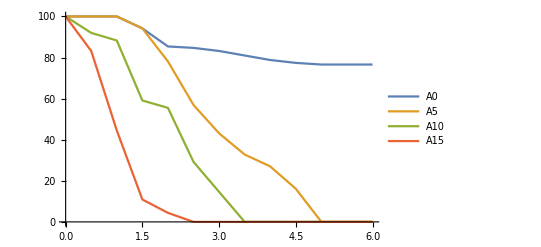

```mathematica
ListLinePlot[{dataA0,dataA5,dataA10,dataA15},DataRange->{0,6}, PlotLegends->{"A0","A5","A10","A15"}]
```

### Data transformation

```mathematica
dataA = Join[{Range[0,6,0.5], ConstantArray[0,13], dataA0}ᵀ,{Range[0,6,0.5], ConstantArray[5,13], dataA5}ᵀ, {Range[0,6,0.5], ConstantArray[10,13], dataA10}ᵀ,{Range[0,6,0.5], ConstantArray[15,13], dataA15}ᵀ]
```

{{0.,0,100},{0.5,0,100},{1.,0,100},{1.5,0,94.2},{2.,0,85.4},{2.5,0,84.7},{3.,0,83.2},{3.5,0,81.},{4.,0,78.8},{4.5,0,77.4},{5.,0,76.6},{5.5,0,76.6},{6.,0,76.6},{0.,5,100},{0.5,5,100},{1.,5,100},{1.5,5,94.2},{2.,5,78.1},{2.5,5,56.9},{3.,5,43.1},{3.5,5,32.8},{4.,5,27},{4.5,5,16.1},{5.,5,0},{5.5,5,0},{6.,5,0},{0.,10,100},{0.5,10,92.},{1.,10,88.3},{1.5,10,59.1},{2.,10,55.5},{2.5,10,29.2},{3.,10,14.6},{3.5,10,0},{4.,10,0},{4.5,10,0},{5.,10,0},{5.5,10,0},{6.,10,0},{0.,15,100},{0.5,15,83.2},{1.,15,44.5},{1.5,15,10.9},{2.,15,4.4},{2.5,15,0},{3.,15,0},{3.5,15,0},{4.,15,0},{4.5,15,0},{5.,15,0},{5.5,15,0},{6.,15,0}}

```mathematica
dataANorm = (dataAᵀ/{1,1,100})ᵀ
```

{{0.,0,1},{0.5,0,1},{1.,0,1},{1.5,0,0.942},{2.,0,0.854},{2.5,0,0.847},{3.,0,0.832},{3.5,0,0.81},{4.,0,0.788},{4.5,0,0.774},{5.,0,0.766},{5.5,0,0.766},{6.,0,0.766},{0.,5,1},{0.5,5,1},{1.,5,1},{1.5,5,0.942},{2.,5,0.781},{2.5,5,0.569},{3.,5,0.431},{3.5,5,0.328},{4.,5,27/100},{4.5,5,0.161},{5.,5,0},{5.5,5,0},{6.,5,0},{0.,10,1},{0.5,10,0.92},{1.,10,0.883},{1.5,10,0.591},{2.,10,0.555},{2.5,10,0.292},{3.,10,0.146},{3.5,10,0},{4.,10,0},{4.5,10,0},{5.,10,0},{5.5,10,0},{6.,10,0},{0.,15,1},{0.5,15,0.832},{1.,15,0.445},{1.5,15,0.109},{2.,15,0.044},{2.5,15,0},{3.,15,0},{3.5,15,0},{4.,15,0},{4.5,15,0},{5.,15,0},{5.5,15,0},{6.,15,0}}

### Approximation and analysis

```mathematica
FindFit[dataA, 100 Exp[-γA x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],{{μ,0.05} ,{β,0.185}},{x,t}, Method->NMinimize]
functionA =  100 Exp[-γA x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
```

{μ→0.0540546,β→0.34094}

100 ⅇ^(0.465025 t (1-ⅇ^(-0.34094 x)-0.34094 x)-0.053 x)

```mathematica
Show[ ListPointPlot3D[dataA],Plot3D[functionA,{x,0,6},{t, 0,15}, AxesLabel->Automatic]]
```

-Graphics3D-

```mathematica
FindFit[dataANorm, Exp[-γA x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],{μ, β},{x,t},Method->NMinimize]
functionANorm =  Exp[-γA x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[dataANorm],Plot3D[functionANorm,{x,0,6},{t, 0,15}, AxesLabel->Automatic]]
(functionANorm/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{x,0,6,0.5},{t, 0,15,5}],1];
Mean@Abs[dataANorm⟦;;,3⟧-%]
```

{μ→0.0540592,β→0.341071}

ⅇ^(0.464709 t (1-ⅇ^(-0.341071 x)-0.341071 x)-0.053 x)

-Graphics3D-

0.247374

## Verapamil

### Data

```mathematica
SetDirectory[NotebookDirectory[]];
test  =Flatten[Import["yeon-data/V0.json"],1]
dataV0 = "Cexp"/.test
γV = "gamma"/.test
dataV50 = "Cexp"/.Flatten[Import["yeon-data/V50.json"],1]
dataV100 = "Cexp"/.Flatten[Import["yeon-data/V100.json"],1]
dataV200 = "Cexp"/.Flatten[Import["yeon-data/V200.json"],1]
```

{T→0,gamma→0.053,t50→1.5,Cexp→{100,100,100,94.1,86.,85.3,83.8,81.6,79.4,77.9,77.2,77.2,77.2}}

{100,100,100,94.1,86.,85.3,83.8,81.6,79.4,77.9,77.2,77.2,77.2}

0.053

{100,100,98.5,86.7,67.6,55.1,28.7,16.2,0,0,0,0,0}

{100,99.3,83.8,71.3,54.4,35.3,13.2,0,0,0,0,0,0}

{100,94.9,76.5,44.9,13.2,0,0,0,0,0,0,0,0}

### Data transformation

```mathematica
dataV = Join[{Range[0,6,0.5], ConstantArray[0,13], dataV0}ᵀ,{Range[0,6,0.5], ConstantArray[50,13], dataV50}ᵀ, {Range[0,6,0.5], ConstantArray[100,13], dataV100}ᵀ,{Range[0,6,0.5], ConstantArray[200,13], dataV200}ᵀ];
dataVNorm = (dataVᵀ/{1,1000,100})ᵀ;
```

### Approximation and analysis

```mathematica
FindFit[dataV, 100 Exp[-γV x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],{μ ,β},{x,t}, Method->NMinimize]
functionV =  100 Exp[-γV x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[dataV],Plot3D[functionV,{x,0,6},{t, 0,200}, AxesLabel->Automatic]]
```

{μ→0.00161759,β→-0.84831}

100 ⅇ^(0.00224782 t (1-ⅇ^(0.84831 x)+0.84831 x)-0.053 x)

-Graphics3D-

```mathematica
FindFit[dataVNorm, {Exp[-γV x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],β>0},{{β,0.000184},{μ,3.83}},{x,t}]
functionVNorm =  Exp[-γV x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[dataVNorm],Plot3D[functionVNorm,{x,0,6},{t, 0,0.2}, AxesLabel->Automatic]]
(functionVNorm/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{x,0,6,0.5},{t, {0,50,100,200}/1000}],1];
Mean@Abs@(dataVNorm⟦;;,3⟧-%)
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{β→0.0000131426,μ→3.76843}

ⅇ^(2.18173×10^10 t (1-ⅇ^(-0.0000131426 x)-0.0000131426 x)-0.053 x)

-Graphics3D-

0.272287

## Diclofenac

### Data

```mathematica
SetDirectory[NotebookDirectory[]];
test  =Flatten[Import["yeon-data/D0.json"],1]
dataD0 = "Cexp"/.test
γD = "gamma"/.test
dataD100 = "Cexp"/.Flatten[Import["yeon-data/D100.json"],1]
dataD300 = "Cexp"/.Flatten[Import["yeon-data/D300.json"],1]
dataD600 = "Cexp"/.Flatten[Import["yeon-data/D600.json"],1]
```

{T→0,gamma→0.053,t50→1.5,Cexp→{100,100,100,100,94.1,86.,84.6,83.8,80.9,78.7,77.9,76.5,76.5}}

{100,100,100,100,94.1,86.,84.6,83.8,80.9,78.7,77.9,76.5,76.5}

0.053

{100,100,100,98.5,86.8,69.9,50.,36.8,26.5,14.7,8.1,0,0}

{100,100,93.4,83.8,54.4,5.88,0,0,0,0,0,0,0}

{100,94.1,72.1,38.2,22.1,5.88,0,0,0,0,0,0,0}

### Data transformation

```mathematica
dataD = Join[{Range[0,6,0.5], ConstantArray[0,13], dataD0}ᵀ,{Range[0,6,0.5], ConstantArray[100,13], dataD100}ᵀ, {Range[0,6,0.5], ConstantArray[300,13], dataD300}ᵀ,{Range[0,6,0.5], ConstantArray[600,13], dataD600}ᵀ];
dataDNorm = (dataDᵀ/{1,1000,100})ᵀ;
```

### Approximation and analysis

```mathematica
FindFit[dataD, 100 Exp[-γD x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],{μ ,β},{x,t}, Method->NMinimize]
functionD =  100 Exp[-γD x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[dataD],Plot3D[functionD,{x,0,6},{t, 0,600}, AxesLabel->Automatic]]
```

{μ→0.000690131,β→-0.569258}

100 ⅇ^(0.00212968 t (1-ⅇ^(0.569258 x)+0.569258 x)-0.053 x)

-Graphics3D-

```mathematica
FindFit[dataDNorm, {Exp[-γD x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],β>0},{{β,0.000182},{μ,1.23}},{x,t}]
functionDNorm =  Exp[-γD x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[dataDNorm],Plot3D[functionDNorm,{x,0,6},{t, 0,0.6}, AxesLabel->Automatic]]
(functionDNorm/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{x,0,6,0.5},{t, {0,100,300,600}/1000}],1];
Mean@Abs@(dataDNorm⟦;;,3⟧-%)
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{β→0.0000102154,μ→1.25323}

ⅇ^(1.20094×10^10 t (1-ⅇ^(-0.0000102154 x)-0.0000102154 x)-0.053 x)

-Graphics3D-

0.271226

## Benzopyrene

### Data

```mathematica
SetDirectory[NotebookDirectory[]];
test  =Flatten[Import["yeon-data/B0.json"],1]
dataB0 = "Cexp"/.test
γB = "gamma"/.test
dataB12 = "Cexp"/.Flatten[Import["yeon-data/B12.json"],1]
dataB25 = "Cexp"/.Flatten[Import["yeon-data/B25.json"],1]
dataB50 = "Cexp"/.Flatten[Import["yeon-data/B50.json"],1]
```

{T→0,gamma→0.053,t50→1.5,Cexp→{100,100,99.3,93.5,85.5,84.8,83.3,81.2,79.,77.5,76.8,76.8,76.8}}

{100,100,99.3,93.5,85.5,84.8,83.3,81.2,79.,77.5,76.8,76.8,76.8}

0.053

```mathematica
{100,100,94.9,77.5,65.9,37.,17.4,9.42,0,0,0,0,0}
```

{100,97.1,77.5,42.8,23.9,5.07,0,0,0,0,0,0,0}

{100,93.5,27.5,4.35,2.18,0.72,0,0,0,0,0,0,0}

### Data transformation

```mathematica
dataB = Join[{Range[0,6,0.5], ConstantArray[0,13], dataB0}ᵀ,{Range[0,6,0.5], ConstantArray[12,13], dataB12}ᵀ, {Range[0,6,0.5], ConstantArray[25,13], dataB25}ᵀ,{Range[0,6,0.5], ConstantArray[50,13], dataB50}ᵀ];
dataBNorm = (dataBᵀ/{1,1000,100})ᵀ;
```

### Approximation and analysis

```mathematica
FindFit[dataB, 100 Exp[-γB x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],{μ ,β},{x,t}, Method->NMinimize]
functionB =  100 Exp[-γB x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[dataB],Plot3D[functionB,{x,0,6},{t, 0,50}, AxesLabel->Automatic]]
```

{μ→0.0241813,β→-0.155426}

100 ⅇ^(1.001 t (1-ⅇ^(0.155426 x)+0.155426 x)-0.053 x)

-Graphics3D-

```mathematica
FindFit[dataBNorm, {Exp[-γB x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],β>0},{{β,0.0000702},{μ,26.5}},{x,t}]
functionBNorm =  Exp[-γB x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[dataBNorm],Plot3D[functionBNorm,{x,0,6},{t, 0,0.05}, AxesLabel->Automatic]]
(functionBNorm/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{x,0,6,0.5},{t, {0,12,25,50}/1000}],1];
Mean@Abs[dataBNorm⟦;;,3⟧-%]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{β→0.0000125798,μ→26.9034}

ⅇ^(1.70005×10^11 t (1-ⅇ^(-0.0000125798 x)-0.0000125798 x)-0.053 x)

-Graphics3D-

0.246363

## Benzopyrene with other models

```mathematica
FindFit[dataBNorm,  {Exp[-(δ*t+γB) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)],μ>0, β>0 , δ>0},{μ,β,δ},{x,t}]
functionB2 =  Exp[-(δ*t+γB) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)]/. %
Show[ ListPointPlot3D[dataBNorm],Plot3D[functionB2,{x,0,6},{t, 0,0.05}, AxesLabel->Automatic]]
(functionB2/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{x,0,6,0.5},{t, {0,12,25,50}/1000}],1];
Mean@Abs[dataBNorm⟦;;,3⟧-%]
```

{μ→1.07866,β→8122.9,δ→25.5364}

ⅇ^(1.63478×10^-8 (1-ⅇ^(-8122.9 t)-8122.9 t) t+(-0.053-25.5364 t) x)

-Graphics3D-

0.273236

```mathematica
FindFit[dataBNorm,  Exp[-(δ* t+γB) x],{δ},{x,t}]
functionB3 =   Exp[-(δ* t+γB) x]/. %
Show[ ListPointPlot3D[dataBNorm],Plot3D[functionB3,{x,0,6},{t, 0,0.05}, AxesLabel->Automatic]]
(functionB3/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{x,0,6,0.5},{t, {0,12,25,50}/1000}],1];
Mean@Abs[dataBNorm⟦;;,3⟧-%]
```

{δ→25.5364}

ⅇ^((-0.053-25.5364 t) x)

-Graphics3D-

0.273236

## Conclusion

The following parameters were obtained for the first model
A: β=0.341071,μ=0.0540592, error = 0.247374 
V: β=0.0000131426,μ=3.76843, error = 0.272287
D: β=0.0000102154,μ=1.25323, error =0.271226
B: β→0.0000125798,μ→26.9034, error =0.246363
The following parameters were obtained with other models for B:
f2: β =  8122.9, δ  = 25.5364, μ = 1.07866, error = 0.273236
f3: δ =25.5364, error = 0.273236